# Normalized Additional Velocity (NAV)

By Davi Rodrigues & Alejandro Hernandez-Arboleda
September, 2022

The method is described in detail in the paper:
“Normalized additional velocity distribution: testing the radial profile of dark matter halos and MOND”
by D.C. Rodrigues,  A.Hernandez-Arboleda & A.Wojnar

## Prelude

```mathematica
saveAllPlots = False; (*Change this to True to save ALL the plots that are generated in THIS notebook. It does not include NAVobservational plots. Saves for specific models are in their respective sections.*)
saveNAVobservationalPlots = False;
saveNAVobservationalTables = False;

pathBaseDirectory = NotebookDirectory[];
pathOutputDirectory = FileNameJoin[{pathBaseDirectory, "Output"}];
pathAuxDirectory = FileNameJoin[{pathBaseDirectory, "AuxiliaryData"}];

SetDirectory @ pathBaseDirectory;

Needs @ "NAVbaseCode`";
Get @ "NAVoptions.wl";
Get @ "NAVobservational.wl";
Get @ "NAVauxiliaryFunctions.wl";
Get["MDC14aux.mx", Path -> pathAuxDirectory] // Quiet; (*If something goes wrong, this file will be generated*)

SetDirectory @ pathOutputDirectory;

savePreviousPlot[fileName_] := If[saveThisPlot || saveAllPlots, 
  Echo @ Export[ToString @ fileName, %]; saveThisPlot = False
];
```

Starting NAVobservational...

"list2RARRot"  0.023919

"distRAR"  17.097

"plotBlueRAR"  19.5145

"plotSigmaRegions"  0.191683

## Brief ΔV^2 analysis

3.0773

{0.910055,3.15399}

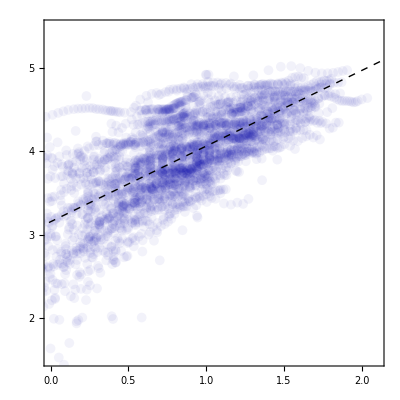

```mathematica
saveThisPlot = False;

dataDeltaVobs = Block[{rawData},
  rawData = Re[{Log10[#1] , Log10[#2]} & @@@ Flatten[gdR[{Rad, Vmiss2}],1]];
  Select[rawData, #[[1]] > 0 &]
];

Clear[b, loga, model, logR, loga0];
model0 = logR + loga0;
loga0 = loga0 /. First@FindFit[dataDeltaVobs,  model0 ,  {loga0} , logR]

Clear[loga];
model = b logR + loga;
{b , loga} = {b, loga} /. FindFit[dataDeltaVobs,  model , {b , loga} , logR]

Show[
  plotBlueZero[
    {Log10[#1], Log10[#2]} & @@@ Flatten[gdR[{Rad, Vmiss2}], 1], 
    PlotRange-> {{-0.0,2.1}, {1.5,5.5}}
  ],
  Plot[
    {
      model
    }, 
    {logR, -1, 3}, 
    PlotStyle->{{Black, Thick, Dashed}, {Black, Thick}, {Black, DotDashed}},
    PlotRange->All
  ]
]

savePreviousPlot["plotDeltaV2analysis.pdf"];
```

## 0. Polynomial approximation

Models considered here :
    r^a -- for monotonic curves
  2 r^a - r^b -- for non - monotonic curves

  Both cases satisfy δV (0) = 0 and δV (1) = 1.
  
  The fits are done considering data between 0.2 < rn < 0.9 .

{0.415394}

{0.376723,1.92178}

{2.24473}

{0.576874,1.65699}

{0.868438}

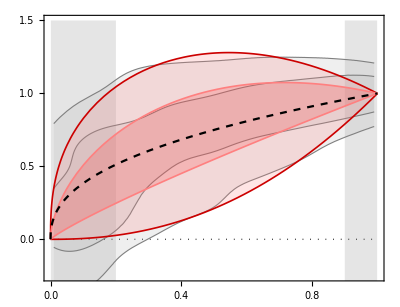

```mathematica
saveThisPlot = False;

Clear[ac];
list2restrictedRARRot = Select[list2RARRot, 0.2 <  #[[1]] < 0.9 &] ;
{ac} ={ac} /. FindFit[list2restrictedRARRot,  r^ac , ac , r]

Clear[a, b, c, d, e, f, g, h];

list = Table[{r, list1InterpCurvesRAR[[4]][r]}, {r,0.2, 0.9, 0.05}];
{c, d} = {c , d}/. FindFit[list, {2 r^c -  r^d},  {c, d}, r]

list = Table[{r, list1InterpCurvesRAR[[3]][r]}, {r,0.2, 0.9, 0.05}];
{b} = {b}/. FindFit[list, r^b,  {b}, r]

list = Table[{r, list1InterpCurvesRAR[[2]][r]}, {r,0.2, 0.9, 0.05}];
{e, f} = {e, f}/. FindFit[list, {2 r^e -  r^f},  {e, f}, r]

list = Table[{r, list1InterpCurvesRAR[[1]][r]}, {r,0.2, 0.9, 0.05}];
{g} = {g}/. FindFit[list, r^g ,  {g}, r]

plotPowerLawModel = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        2 rn^c - rn^d, 
        2 rn^e -  rn^f,  
        rn^b, 
        rn^g
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Red, 0.2], Thickness @ 0.003},
        {Lighter[Red, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Red, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Red, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ],
    Plot[rn^ac, {rn,0,1}, PlotStyle -> {Black, Dashed}]
  }
]

savePreviousPlot["plotPowerLawModel.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[#^g &, 2 #^e - #^f &, 1]
efficiencyNAV[#^b &, 2 #^c - #^d &, 2]
efficiencyNAVtotal[#^g &, 2 #^e - #^f &, #^b &, 2 #^c - #^d &]
```

{0.807192,0.901866,0.0946741}

{0.908244,0.945761,0.0375164}

{0.857718,0.923813,0.0660953}

## I. ArcTan models

## ArcTan

plotArctanGrayRed:

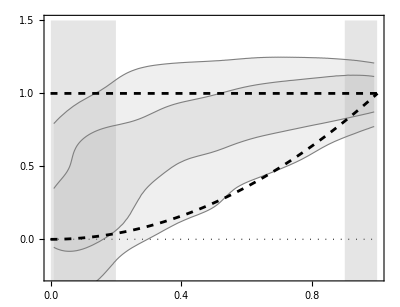

```mathematica
δVarctan[rn_, rtn_] = ArcTan[rn/rtn]^2/ArcTan[1/rtn]^2;

δVarctanLimit1[rn_] = Limit[δVarctan[rn, rtn], rtn -> ∞];
δVarctanLimit2[rn_] = Limit[δVarctan[rn, rtn], rtn -> 0];
  

plotArctanGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVarctanLimit1[rn], 
        δVarctanLimit2[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotArctanGrayRed:"];
Print@plotArctanGrayRed;
```

Performing the optimization.

rtn 1σ bounds:   {0.0358811,0.373523}

rtn 2σ bounds:   {0.001,22553.4}

plotArctanGlobalBestFit:

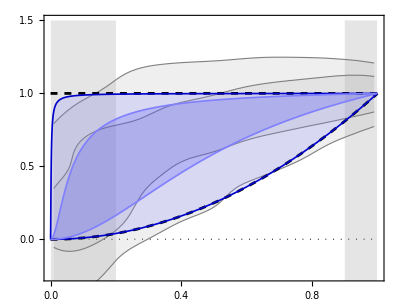

```mathematica
saveThisPlot = False;

(* DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];

Clear[chi2Upper, chi2Lower];
chi2Upper[rtn_?NumberQ, nσ_] := NIntegrate[
  (upperBound[nσ][rn] - δVarctan[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rtn_?NumberQ, nσ_] := NIntegrate[
  (lowerBound[nσ][rn] - δVarctan[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* EXECUTION *)

Echo["Performing the optimization."];

rtnUpper[2] = rtn /. NMinimize[{chi2Upper[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnUpper[1] = rtn /. NMinimize[{chi2Upper[rtn,1],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[2] = rtn /. NMinimize[{chi2Lower[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[1] = rtn /. NMinimize[{chi2Lower[rtn,1],rtn>0.001},{rtn,0,10}][[2]];

Echo[{rtnUpper[1], rtnLower[1]}, "rtn 1σ bounds: "];
Echo[{rtnUpper[2], rtnLower[2]}, "rtn 2σ bounds: "];

plotArctanGlobalBestFit = Show[
  {
    plotArctanGrayRed,
    Plot[
      {
        δVarctan[rn, rtnUpper @ 2],
        δVarctan[rn, rtnUpper @ 1],
        δVarctan[rn, rtnLower @ 2],
        δVarctan[rn, rtnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotArctanGlobalBestFit:"];
Print@plotArctanGlobalBestFit;

savePreviousPlot["plotArctanGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVarctan[#, rtnLower@ 1] &, δVarctan[#, rtnUpper@ 1] &, 1]
efficiencyNAV[δVarctan[#, rtnLower@ 2] &, δVarctan[#, rtnUpper@ 2] &, 2]
efficiencyNAVtotal[δVarctan[#, rtnLower@ 1] &, δVarctan[#, rtnUpper@ 1] &, δVarctan[#, rtnLower@ 2] &, δVarctan[#, rtnUpper@ 2] &]
```

{0.694453,0.764207,0.0697544}

{0.704059,0.708604,0.00454534}

{0.699256,0.736406,0.0371499}

### Comparison with individual fits

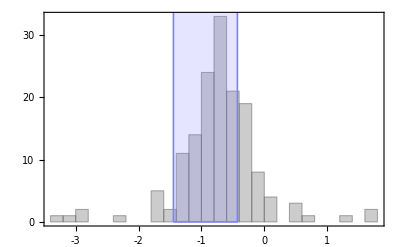

```mathematica
saveThisPlot = False;

resultsArctan = Get["../AuxiliaryData/arctan-GY-1-MAGMAtableResults.m"]; (*These results only inlcude the 153 RAR galaxies*)
headerArctan = First @ resultsArctan;
resultsArctanData = Drop[resultsArctan, 1];
colRt = First @ Flatten @ Position[headerArctan, "Rt"];
listRtn = resultsArctanData[[All, colRt]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rtnUpper @ 1, 0}, {Log10@rtnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRtn, 
  {0.2}, 
  PlotRange -> All,
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramArctan.pdf"];
```

```mathematica
colChi2Arctan = First @ Flatten @ Position[headerArctan, "Chi2"];
colVChi2Arctan = First @ Flatten @ Position[headerArctan, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listArctanChi2 = resultsArctanData[[All, colChi2Arctan]];
listArctanVChi2 = resultsArctanData[[All, colVChi2Arctan]];
Echo[{Median @ listArctanChi2, Median @ listArctanVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listArctanChi2, Total @listArctanVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {8.89515,8.49742}

Total {Chi2, Chi2Eff}:   {7485.48,7040.94}

## ArcTanHalf

plotArctanHalfGrayRed:

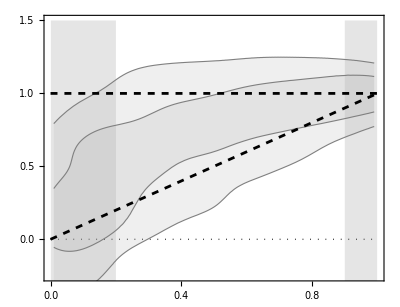

```mathematica
δVarctanHalf[rn_, rtn_] = ArcTan[rn/rtn]/ArcTan[1/rtn];

δVarctanHalfLimit1[rn_] = Limit[δVarctanHalf[rn, rtn], rtn -> ∞];
δVarctanHalfLimit2[rn_] = Simplify[Limit[δVarctanHalf[rn, rtn], rtn -> 0], rn > 0];
  

plotArctanHalfGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVarctanHalfLimit1[rn], 
        δVarctanHalfLimit2[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotArctanHalfGrayRed:"];
Print@plotArctanHalfGrayRed;
```

Performing the optimization.

rtn 1σ bounds:   {0.0696424,1.24667}

rtn 2σ bounds:   {0.001,43285.4}

plotArctanHalfGlobalBestFit:

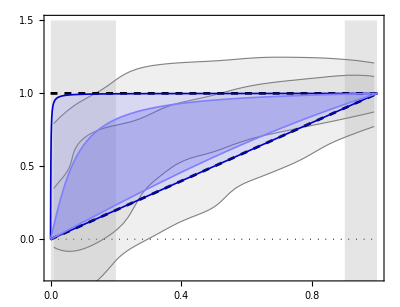

```mathematica
saveThisPlot = False;

(* DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];

Clear[chi2Upper, chi2Lower];
chi2Upper[rtn_?NumberQ, nσ_] := NIntegrate[
  (upperBound[nσ][rn] - δVarctanHalf[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rtn_?NumberQ, nσ_] := NIntegrate[
  (lowerBound[nσ][rn] - δVarctanHalf[rn,rtn])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* EXECUTION *)

Echo["Performing the optimization."];

rtnUpper[2] = rtn /. NMinimize[{chi2Upper[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnUpper[1] = rtn /. NMinimize[{chi2Upper[rtn,1],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[2] = rtn /. NMinimize[{chi2Lower[rtn,2],rtn>0.001},{rtn,0,10}][[2]];
rtnLower[1] = rtn /. NMinimize[{chi2Lower[rtn,1],rtn>0.001},{rtn,0,10}][[2]];

Echo[{rtnUpper[1], rtnLower[1]}, "rtn 1σ bounds: "];
Echo[{rtnUpper[2], rtnLower[2]}, "rtn 2σ bounds: "];

plotArctanHalfGlobalBestFit = Show[
  {
    plotArctanHalfGrayRed,
    Plot[
      {
        δVarctanHalf[rn, rtnUpper @ 2],
        δVarctanHalf[rn, rtnUpper @ 1],
        δVarctanHalf[rn, rtnLower @ 2],
        δVarctanHalf[rn, rtnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotArctanHalfGlobalBestFit:"];
Print@plotArctanHalfGlobalBestFit;

savePreviousPlot["plotArctanHalfGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
Off[NIntegrate::izero];
efficiencyNAV[δVarctanHalf[#, rtnLower@ 1] &, δVarctanHalf[#, rtnUpper@ 1] &, 1]
efficiencyNAV[δVarctanHalf[#, rtnLower@ 2] &, δVarctanHalf[#, rtnUpper@ 2] &, 2]
Mean[{%, %%}]
On[NIntegrate::izero];
```

{0.709364,0.78197,0.0726068}

{0.489001,0.489001,0.}

{0.599182,0.635486,0.0363034}

The variable areaModelOut at 2σ is indeed null, hence the Off is used above.

### Comparison with individual fits

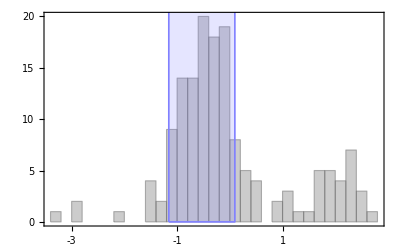

```mathematica
saveThisPlot = False;

resultsArctanHalf = Get["../AuxiliaryData/arctanHalf-GY-1-MAGMAtableResults.m"]; (*These results only inlcude the 153 RAR galaxies*)
headerArctanHalf = First @ resultsArctanHalf;
resultsArctanHalfData = Drop[resultsArctanHalf, 1];
colRt = First @ Flatten @ Position[headerArctanHalf, "Rt"];
listRtnHalf = resultsArctanHalfData[[All, colRt]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rtnUpper @ 1, 0}, {Log10@rtnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRtnHalf, 
  {0.2}, 
  PlotRange -> All,
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramArctanHalf.pdf"];
```

As expected, there are several cases with rtn > 10, and even many cases with rtn > 100. The latter reached the maximum

```mathematica
colChi2ArctanHalf = First @ Flatten @ Position[headerArctanHalf, "Chi2"];
colVChi2ArctanHalf = First @ Flatten @ Position[headerArctanHalf, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listArctanHalfChi2 = resultsArctanHalfData[[All, colChi2ArctanHalf]];
listArctanHalfVChi2 = resultsArctanHalfData[[All, colVChi2ArctanHalf]];
Echo[{Median @ listArctanHalfChi2, Median @ listArctanHalfVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listArctanHalfChi2, Total @listArctanHalfVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {18.9855,17.7199}

Total {Chi2, Chi2Eff}:   {9867.32,9434.33}

## II. Burkert

plotBurkertGrayRed:

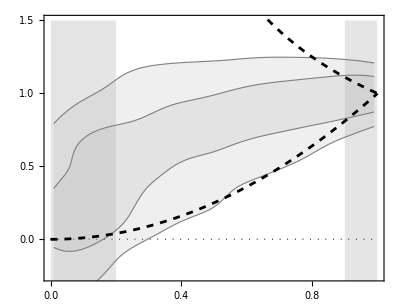

```mathematica
ρbrkt[rn_, rcn_, ρ0_] = ρ0/((1+rn/rcn)(1+rn^2/rcn^2));
Mbrkt[rn_, rcn_, ρ0_] = 4 π Rmax^3 Integrate[ρbrkt[rnprime,rcn,ρ0] rnprime^2,{rnprime,0,rn}, Assumptions-> {rn>0, rcn>0}];

VVbrkt[rn_, rcn_, ρ0_, Rmax_] = (G / Rmax) * Mbrkt[rn, rcn, ρ0] / rn;

δVbrkt[rn_, rcn_] = FullSimplify[
  VVbrkt[rn, rcn, ρ0, Rmax] / VVbrkt[1, rcn, ρ0, Rmax],
  Assumptions -> {0 < rn < 1, 0 < rcn < 1, 0 < Rmax}
];

plotBurkertGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        rn^2, (*These are the limiting curves for Burkert.*)
        1/rn
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotBurkertGrayRed:"];
Print@plotBurkertGrayRed;
```

Performing the optimization.

rcn 1σ bounds:   {0.196103,0.58212}

rcn 2σ bounds:   {0.116784,34.9365}

plotBurkertGlobalBestFit:

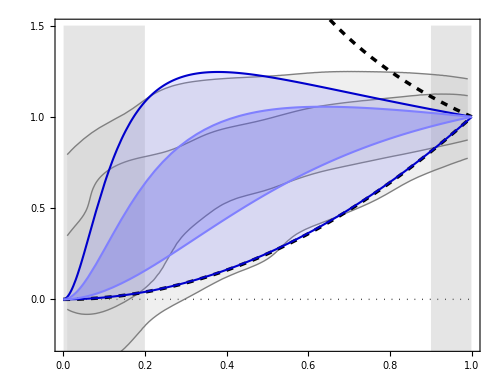

```mathematica
saveThisPlot = False;

Clear[chi2Upper, chi2Lower];
chi2Upper[rcn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rcn_?NumberQ, nσ_]:= chi2Lower[rcn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVbrkt[rn,rcn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd=0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

rcnUpper[2] = rcn /. NMinimize[{chi2Upper[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnUpper[1] = rcn /. NMinimize[{chi2Upper[rcn,1],rcn>0},{rcn,0,10}][[2]];
rcnLower[2] = rcn /. NMinimize[{chi2Lower[rcn,2],rcn>0},{rcn,0,10}][[2]];
rcnLower[1] = rcn /. NMinimize[{chi2Lower[rcn,1],rcn>0},{rcn,0,10}][[2]];

Echo[{rcnUpper[1], rcnLower[1]}, "rcn 1σ bounds: "];
Echo[{rcnUpper[2], rcnLower[2]}, "rcn 2σ bounds: "];

plotBurkertGlobalBestFit = Show[
  {
    plotBurkertGrayRed,
    Plot[
      {
        δVbrkt[rn, rcnUpper @ 2],
        δVbrkt[rn, rcnUpper @ 1],
        δVbrkt[rn, rcnLower @ 2],
        δVbrkt[rn, rcnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotBurkertGlobalBestFit:"];
Print @ plotBurkertGlobalBestFit;

savePreviousPlot["plotBurkertGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVbrkt[#, rcnLower@ 1] &, δVbrkt[#, rcnUpper@ 1] &, 1]
efficiencyNAV[δVbrkt[#, rcnLower@ 2] &, δVbrkt[#, rcnUpper@ 2] &, 2]
Mean[{%, %%}]
```

{0.738335,0.833853,0.0955181}

{0.86247,0.878446,0.0159759}

{0.800403,0.85615,0.055747}

### Comparison with individual fits

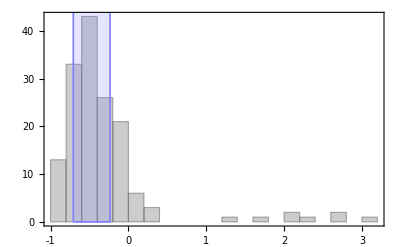

```mathematica
saveThisPlot = False;

resultsBurkert = Get["../AuxiliaryData/Burkert-GY-05-06-MAGMAtableResults.m"]; (*These results include all 175 galaxies*)
headerBurkert = First @ resultsBurkert;
resultsBurkertData = Drop[resultsBurkert, 1];
colRc = First @ Flatten @ Position[headerBurkert, "rc"];
listRcn = DeleteCases[resultsBurkertData[[All, colRc]] / (rmax /@ Range @ 175), _/Last[{}]] // Quiet;
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rcnUpper @ 1, 0}, {Log10@rcnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRcn, 
  {0.2}, 
  PlotRange -> {All, All}, (*There are a few galaxies beyond 1*)
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramBurkert.pdf"];
```

As expected, there are not many cases of rcn too small or too large.

```mathematica
colChi2Burkert = First @ Flatten @ Position[headerBurkert, "Chi2"];
colVChi2Burkert = First @ Flatten @ Position[headerBurkert, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listBurkertChi2 = resultsBurkertData[[All, colChi2Burkert]];
listBurkertVChi2 = resultsBurkertData[[All, colVChi2Burkert]];
Echo[{Median @ listBurkertChi2, Median @ listBurkertVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listBurkertChi2, Total @listBurkertVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {8.1357,8.02053}

Total {Chi2, Chi2Eff}:   {8238.22,7693.9}

## III. NFW

### III.1 NFW definition and limiting cases

rn

1/rn

plotNFWGrayRed:

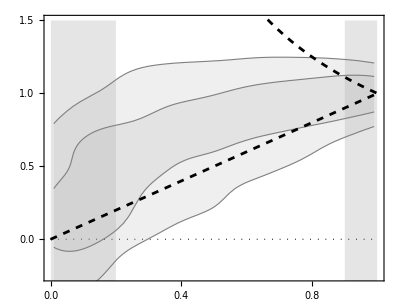

```mathematica
ρnfw[rn_, rsn_, ρs_] = ρs/(rn/rsn(1+rn/rsn)^2);
Mnfw[rn_, rsn_, ρs_] = 4 π Rmax^3 Integrate[ρnfw[rnprime, rsn, ρs] rnprime^2, {rnprime, 0, rn}, Assumptions-> {rn>0, rsn>0}];

VVnfw[rn_, rsn_, ρs_, Rmax_] = (G / Rmax) * Mnfw[rn, rsn, ρs] / rn;

δVnfw[rn_, rsn_] = FullSimplify[
  VVnfw[rn, rsn, ρs, Rmax] / VVnfw[1, rsn, ρs, Rmax],
  Assumptions -> {0 < rn < 1, 0 < Rmax}
];

δVnfwLargeRsn[rn_] = Limit[δVnfw[rn, rsn], rsn -> ∞]
δVnfwSmallRsn[rn_] = Limit[δVnfw[rn, rsn], rsn -> 0]
plotNFWGrayRed = Show[
  {
    plotBackground[1.5],
    plotSigmaRegionsRAR,
    Plot[
      {
        δVnfwLargeRsn[rn], 
        δVnfwSmallRsn[rn]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Thickness[0.005], Black, Dashed}}
    ]
  }
];

Echo["plotNFWGrayRed:"];
Print@plotNFWGrayRed;
```

Performing the optimization.

rsn 1σ bounds:   {0.327763,4.91399}

rsn 2σ bounds:   {0.150412,24790.}

plotNFWGlobalBestFit:

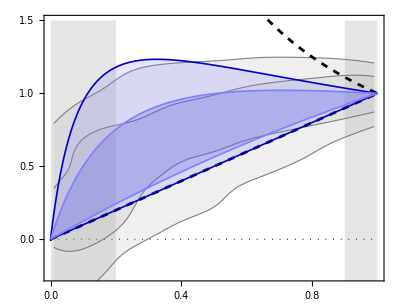

```mathematica
saveThisPlot = False;

Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, nσ_]:= (*chi2Upper[rcn, nσ] =*) NIntegrate[
  (upperBound[nσ][rn] - δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];

chi2Lower[rsn_?NumberQ, nσ_]:= chi2Lower[rsn, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVnfw[rn,rsn])^2, 
  {rn,rnStart,rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing"-> 0},
  WorkingPrecision->10, 
  PrecisionGoal->3, 
  AccuracyGoal->Infinity, 
  MaxRecursion->10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

Clear[rsnUpper, rsnLower];

rsnUpper[2] = rsn /. NMinimize[{chi2Upper[rsn,2], rsn > 0}, {rsn, 0, 1}][[2]];
rsnUpper[1] = rsn /. NMinimize[{chi2Upper[rsn,1], rsn > 0}, {rsn, 0, 1}][[2]];
rsnLower[2] = rsn /. NMinimize[{chi2Lower[rsn,2], rsn > 0}, {rsn, 10, 10000}][[2]];
rsnLower[1] = rsn /. NMinimize[{chi2Lower[rsn,1], rsn > 0}, {rsn, 10, 10000}][[2]];

Echo[{rsnUpper[1], rsnLower[1]}, "rsn 1σ bounds: "];
Echo[{rsnUpper[2], rsnLower[2]}, "rsn 2σ bounds: "];

plotNFWGlobalBestFit = Show[
  {
    plotNFWGrayRed,
    Plot[
      {
        δVnfw[rn, rsnUpper @ 2],
        δVnfw[rn, rsnUpper @ 1],
        δVnfw[rn, rsnLower @ 2],
        δVnfw[rn, rsnLower @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotNFWGlobalBestFit:"];
plotNFWGlobalBestFit

savePreviousPlot["plotNFWGlobalBestFit.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVnfw[#, rsnLower@ 1] &, δVnfw[#, rsnUpper@ 1] &, 1]
efficiencyNAV[δVnfw[#, rsnLower@ 2] &, δVnfw[#, rsnUpper@ 2] &, 2]
Mean[{%, %%}]
```

{0.771351,0.843344,0.0719928}

{0.633047,0.648073,0.0150251}

{0.702199,0.745708,0.0435089}

### Comparison with the rsn distribution found from the individual NFW fits

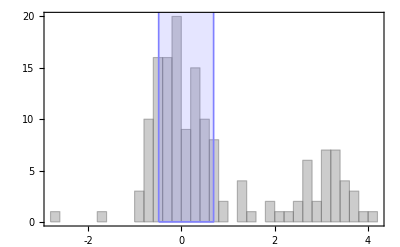

```mathematica
saveThisPlot = False;

resultsNFW = Get["../AuxiliaryData/NFW-GY-05-06-v2-MAGMAtableResults.m"]; (*These results include all 175 galaxies*)
headerNFW = First @ resultsNFW;
resultsNFWData = Drop[resultsNFW, 1];
colRs = First @ Flatten @ Position[headerNFW, "rS"];
resultsNFWDataRAR = Delete[resultsNFWData,  GalaxiesOutsideRAR];
listRsnRAR = resultsNFWDataRAR[[All, colRs]] / (rmax153 /@ Range @ 153);
rectangle = {
  EdgeForm[{Lighter[Blue, 0.5], Thickness @ 0.003}],
  Lighter[Blue, 0.5],
  Opacity @ 0.2,
  Rectangle[{Log10@rsnUpper @ 1, 0}, {Log10@rsnLower @ 1, 100}]
};

Histogram[
  Log10 @ listRsnRAR, 
  {0.2}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False, 
  Epilog -> {rectangle},
  histoOptions
]

savePreviousPlot["histogramNFW.pdf"];
```

```mathematica
colChi2NFW = First @ Flatten @ Position[headerNFW, "Chi2"];
colVChi2NFW = First @ Flatten @ Position[headerNFW, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listNFWChi2 = resultsNFWData[[All, colChi2NFW]];
listNFWVChi2 = resultsNFWData[[All, colVChi2NFW]];
Echo[{Median @ listNFWChi2, Median @ listNFWVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listNFWChi2, Total @listNFWVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {16.0402,14.8832}

Total {Chi2, Chi2Eff}:   {10371.7,9796.13}

## IV. MOND without approximations (153 galaxies, “MondRaw”)

a0 =   1

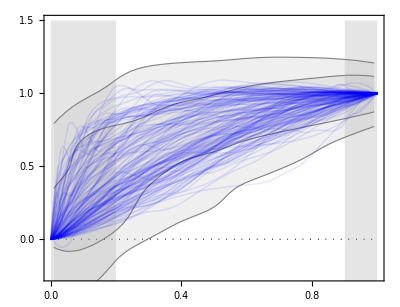

```mathematica
saveThisPlot = False;

Clear[a0, ΔVVmodel, VVmodel, δVVmodel];

saveThisPlot = False; (*Change this to True to save it*)

v2MondRaw[R_, gal_] := R kpc aBar[R, gal]/(1 - ⅇ^(-√(RealAbs[aBar[R, gal]]/a0)));

Δv2MondRaw[R_, gal_] := v2MondRaw[R, gal] - aBar[R, gal] R kpc ;

δv2MondRaw[rn_, gal_] := If[gdR["Rad", gal]=={}, 
  {}, 
  Δv2MondRaw[rn rmax[gal], gal] / Δv2MondRaw[rmax[gal], gal]
];

Echo[a0 = 1, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δv2MondRaw[rn, #]& /@ Range@175], {rn,0,1}, 
    PlotStyle-> Directive[Opacity[0.1],Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmonda01.pdf"];
```

a0 =   1.×10^-15

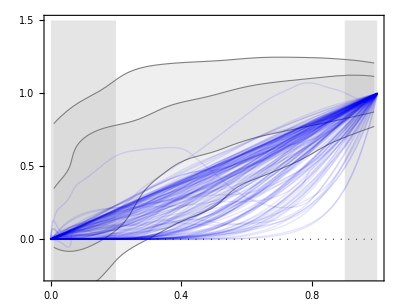

```mathematica
saveThisPlot = False;

Echo[a0 = 1. 10^-15, "a0 = "];
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  Plot[
    Evaluate[δv2MondRaw[rn, #]& /@ Range@175], {rn,0,1},  
    PlotStyle -> Directive[Opacity[0.1], Blue, Thick], PlotRange -> All
  ]
]

savePreviousPlot["plotdeltaVmonda015.pdf"];
```

The galaxy with a bump above 1 has the number 114. At about rn = 0.8 it has a local minimum in its acceleration.

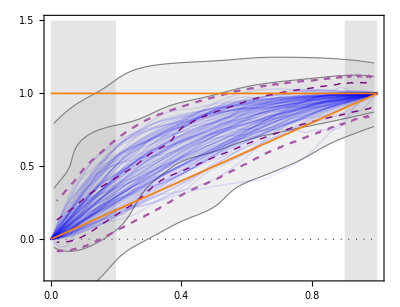

```mathematica
saveThisPlot = False;

a0 = 1.2 10^-13;
Clear @ list2δv2MondRaw;
list2δv2MondRaw[gal_] := If[
  gdR["Rad", gal] == {},
  {},
  Table[{rn, δv2MondRaw[rn, gal]}, {rn, RandomReal[1,70]}]
];
list2δv2MondRawAll = Flatten[DeleteCases[list2δv2MondRaw /@ Range @ 175, {}], 1];

distMondRaw = distributionSilverman @ list2δv2MondRawAll;

pdfValuenSigmaMondRaw[n_?NumberQ] := FindHDPDFValues[distMondRaw, nSigmaProbability[n]];

plotMondRawSigma[n_] := plotMondRawSigma[n] = Block[{pdfValue, contourStyle},
  pdfValue = pdfValuenSigmaMondRaw[n];
  Which[
    n == 1, contourStyle = Directive[Purple, Dashed, Thick], 
    n == 2, contourStyle = Directive[Lighter @ Purple, Dashed],
    True, Automatic
  ];
  ContourPlot[
    PDF[distMondRaw, {x,y}] == pdfValue, 
    {x, 0, 1}, {y, -1, 5},
    PerformanceGoal -> "Quality", 
    ContourStyle -> contourStyle
  ]
];

plotMondRawCurves = Plot[
  Evaluate[δv2MondRaw[rn, #] & /@ Range@122], 
  {rn, 0, 1}, 
  PlotRange -> All, 
  PlotStyle -> Directive[Opacity[0.1],
  Blue, 
  Thick]
];

plotMondRawContours = Show[
  {plotMondRawSigma[1], 
  plotMondRawSigma[2]}
];
  
Show[
  plotBackground[1.5],
  plotSigmaRegionsRAR,
  plotMondRawCurves,
  plotMondRawContours,
  Plot[{rn, 1}, {rn, 0, 1}, PlotStyle -> {{Thickness[0.003], Orange}}]
]

savePreviousPlot["plotdeltaVmondPrincipal.pdf"];
```

### NAV efficiency

```mathematica
DistributeDefinitions["NAVbaseCode`"];
DistributeDefinitions["NAVbaseCode`Private`"];

EchoTiming[
{rI[1], rD[1], rI[2], rD[2]} = Parallelize[{
  regionIntersection[plotMondRawSigma[1],1], 
  regionDifference[plotMondRawSigma[1],1],
  regionIntersection[plotMondRawSigma[2],2],
  regionDifference[plotMondRawSigma[2],2]
  }]
];

efficiencyNAV[1]
efficiencyNAV[2]
efficiencyNAVtotal[]
```

147.265

0.521958

0.547326

0.534642

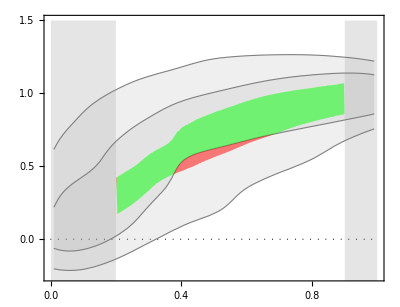

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[1] /. Region[x__] :> Region[Style[x,Opacity[0.5],Green]], rD[1]/. Region[x__] :> Region[Style[x, Opacity[0.5],Red] ]]
```

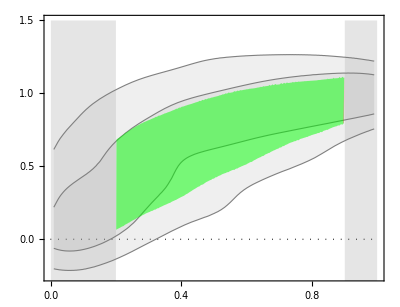

```mathematica
Show[plotBackground[1.5], plotSigmaRegionsRARNoBulge,rI[2] /. Region[x__] :> Region[Style[x,Opacity[0.5], Green]], rD[2]/. Region[x__] :> Region[Style[x, Opacity[0.5], Red] ]]
```

### Comparison with individual fits - Gaussian fits on Y.

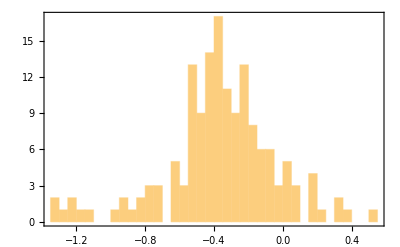

```mathematica
saveThisPlot = False;

resultsMond = Get["../AuxiliaryData/MONDRAR-Fxa0-GY-05-06-MAGMAtableResults.m"]; (*These results include 153 galaxies*)
headerMond = First @ resultsMond;
resultsMondData = Drop[resultsMond, 1];
colYDMond = First @ Flatten @ Position[headerMond, "YD"];
listYDMond = resultsMondData[[All, colYDMond]] ;

Histogram[
  Log10@listYDMond, 
  {0.05}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False
]

savePreviousPlot["histogramMond.pdf"];
```

```mathematica
Median[Log10@listYDMond]
Mean[Log10@listYDMond]
StandardDeviation[Log10@listYDMond]
```

-0.357823

-0.361852

0.322056

```mathematica
colChi2Mond = First @ Flatten @ Position[headerMond, "Chi2"];
colVChi2Mond = First @ Flatten @ Position[headerMond, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listMondChi2 = resultsMondData[[All, colChi2Mond]];
listMondVChi2 = resultsMondData[[All, colVChi2Mond]];
Echo[{Median @ listMondChi2, Median @ listMondVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listMondChi2, Total @listMondVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {59.5866,47.6298}

Total {Chi2, Chi2Eff}:   {32188.4,30334.9}

### Comparison with individual fits - Gaussian fits on Y and D.

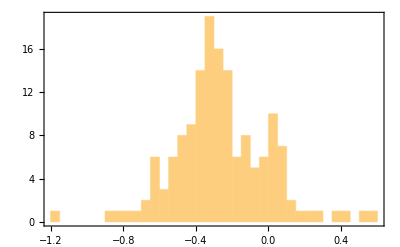

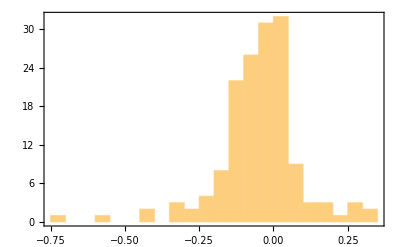

```mathematica
saveThisPlot = False;

resultsMondGD = Get["../AuxiliaryData/MONDRAR-Fxa0-GY-05-06-GD-MAGMAtableResults.m"]; (*These results include 153 galaxies*)
headerMondGD = First @ resultsMondGD;
resultsMondDataGD = Drop[resultsMondGD, 1];
colYDMondGD = First @ Flatten @ Position[headerMondGD, "YD"];
coldf2MondGD = First @ Flatten @ Position[headerMondGD, "df2"];
listYDMondGD = resultsMondDataGD[[All, colYDMond]] ;
listdf2MondGD = resultsMondDataGD[[All, coldf2MondGD]] ;

Histogram[
  Log10@listYDMondGD, 
  {0.05}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False
]

Histogram[
  Log10@listdf2MondGD, 
  {0.05}, 
  PlotRange -> {All, All}, 
  Frame -> True, 
  Axes -> False
]

savePreviousPlot["histogramMondGD.pdf"];
```

```mathematica
Median[Log10@listYDMondGD]
Mean[Log10@listYDMondGD]
StandardDeviation[Log10@listYDMondGD]
```

-0.284471

-0.259147

0.25943

```mathematica
Median[Log10@listdf2MondGD]
Mean[Log10@listdf2MondGD]
StandardDeviation[Log10@listdf2MondGD]
```

-0.0392137

-0.0489561

0.138621

```mathematica
colChi2MondGD = First @ Flatten @ Position[headerMondGD, "Chi2"];
colVChi2MondGD = First @ Flatten @ Position[headerMondGD, "V-Chi2"];(*Chi2 only due to velocity, no priors, standard chi2*)
listMondGDChi2 = resultsMondDataGD[[All, colChi2MondGD]];
listMondGDVChi2 = resultsMondDataGD[[All, colVChi2MondGD]];
Echo[{Median @ listMondGDChi2, Median @ listMondGDVChi2}, "Median {Chi2, Chi2Eff}: "];
Echo[{Total @ listMondGDChi2, Total @listMondGDVChi2}, "Total {Chi2, Chi2Eff}: "];
```

Median {Chi2, Chi2Eff}:   {37.0748,29.5694}

Total {Chi2, Chi2Eff}:   {14600.6,12574.}

## V. DC 14

```mathematica
Clear[X, ρ, α,γ,β]
α = 2.94 - Log10[(10^(X + 2.33))^-1.08 + (10^(X + 2.33))^2.29];
β = 4.23 + 1.34 X + 0.26 X^2;
γ = - 0.06 + Log10[(10^(X + 2.56))^-0.68 + (10^(X+2.56))];
ρDC14[rn_, rsn_, ρs_, X_] = ρs/((rn/rsn)^γ(1+ (rn/rsn)^α)^((β-γ)/α));
```

```mathematica
X100min = -410;
X100max = -130;
Xmin = X100min/100.;
Xmax = X100max/100.;

(*Clear[MDC14aux]; *) (*Uncomment this to recompute and export MDC14aux.*)
If[DownValues@MDC14aux === {}, 
  SetSharedFunction[MDC14aux];
  ParallelTable[
    MDC14aux[rn_, rsn_, ρs_, X100] = 4 π Rmax^3 Integrate[
      ρDC14[rnprime, rsn, ρs, X100 / 100] rnprime^2, {rnprime, 0, rn}, 
      Assumptions -> {rn > 0, rsn > 0}
    ], 
    {X100, X100min, X100max, 1}
  ];
  DumpSave["../AuxiliaryData/MDC14aux.mx", MDC14aux]
];
```

```mathematica
Clear[MDC14, VVDC14, δVDC14];

iRound[x_] = IntegerPart[Round[x, 0.01] 100];

MDC14[rn_, rsn_, ρs_, X_] := MDC14aux[rn, rsn, ρs, iRound[X]];

VVDC14[rn_, rsn_, ρs_, X_] := G/(rn Rmax) MDC14[rn, rsn, ρs, X] ;

δVDC14[rn_, rsn_, X_] := δVDC14[rn, rsn, X] = Simplify[
  VVDC14[rn, rsn, ρs, X]/VVDC14[1, rsn, ρs, X],
  Assumptions -> {0 <= rn <= 1,  rsn > 0, Rmax > 0}
];
```

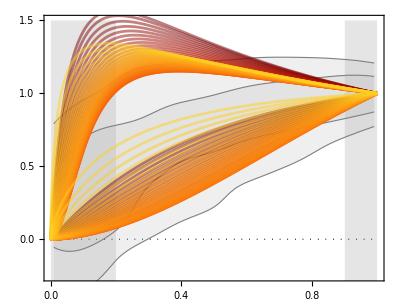

```mathematica
saveThisPlot = False;

Clear[plotDC14GrayRed1];
plotDC14GrayRed1[X_] := 
Show[
  {
    Plot[
      {
        δVDC14[rn,1,X], 
        δVDC14[rn,0.1,X]
      },
      {rn, 0, 1},
      PlotRange -> All,
      PlotStyle -> {{Opacity[0.5], Thickness[0.005], ColorData[ "SolarColors"][(X - Xmin)/(Xmax - Xmin)]}}
    ]
  }
];

Show[{plotBackground[1.5],
    plotSigmaRegionsRAR,Table[plotDC14GrayRed1[X], {X, Xmin, Xmax, 0.05}]}]
    
savePreviousPlot["plotDC14SunColor.pdf"];
```

These two definitions below are important only if the NFW and Burkert sections were not run

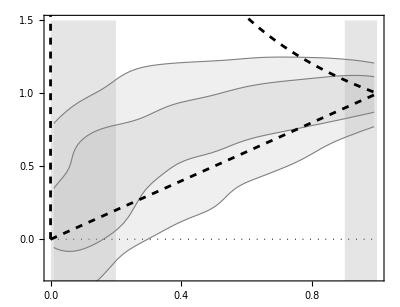
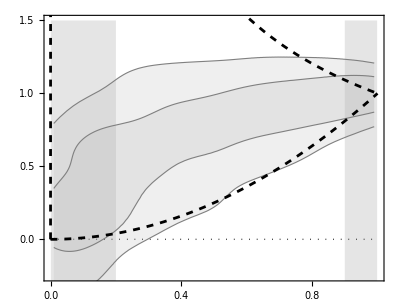
```mathematica
plotNFWGrayRed = -Graphics-;
plotBurkertGrayRed=-Graphics-;
```

```mathematica
Clear[chi2Upper, chi2Lower];
chi2Upper[rsn_?NumberQ, X_, nσ_]:= chi2Upper[rsn, X, nσ] =  NIntegrate[
  (upperBound[nσ][rn] - δVDC14[rn, rsn, X])^2,
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  PrecisionGoal -> 4, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];

chi2Lower[rsn_?NumberQ, X_, nσ_] := chi2Lower[rsn, X, nσ] = NIntegrate[
  (lowerBound[nσ][rn]- δVDC14[rn,rsn, X])^2, 
  {rn, rnStart, rnEnd}, 
  Method-> {Automatic, "SymbolicProcessing" -> 0},
  PrecisionGoal -> 4, 
  AccuracyGoal -> Infinity, 
  MaxRecursion -> 10
];


(* SPECIFIC DEFINITIONS *)

rnStart = 0.2;
rnEnd = 0.9;

lowerBound[1] = list1InterpCurvesRAR[[1]];
upperBound[1] = list1InterpCurvesRAR[[2]];
lowerBound[2] = list1InterpCurvesRAR[[3]];
upperBound[2] = list1InterpCurvesRAR[[4]];


(* EXECUTION *)

Echo["Performing the optimization."];

ClearAll[rsnUpper, rsnLower];
rsnUpper[2] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 2], 10^3>rsn>0.01, Xmin < X < Xmax}, {rsn, X}, 
  MaxIterations -> 500, 
  PrecisionGoal -> 4, 
  AccuracyGoal -> ∞
][[2]];
rsnUpper[1] :=  {rsn, X} /. NMinimize[{chi2Upper[rsn, X, 1], 10^3>rsn>0.01, Xmin < X < Xmax}, {rsn, X},
  MaxIterations -> 500, 
  PrecisionGoal -> 4, 
  AccuracyGoal -> ∞
][[2]];
rsnLower[2] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 2], 10^3>rsn>0.01, Xmin < X < Xmax}, {rsn, X},
  MaxIterations -> 500, 
  PrecisionGoal -> 4, 
  AccuracyGoal -> ∞
][[2]];
rsnLower[1] :=  {rsn, X} /. NMinimize[{chi2Lower[rsn, X, 1], 10^3>rsn>0.01, Xmin < X < Xmax}, {rsn, X},
  MaxIterations -> 500, 
  PrecisionGoal -> 4, 
  AccuracyGoal -> ∞
][[2]];

{rsnUpperR[2], rsnUpperR[1], rsnLowerR[2], rsnLowerR[1]} = Parallelize[
  {rsnUpper[2], rsnUpper[1], rsnLower[2], rsnLower[1]}
];

Echo[{rsnUpperR[1], rsnLowerR[1]}, "{rsn, X} 1σ bounds: "];
Echo[{rsnUpperR[2], rsnLowerR[2]}, "{rsn, X} 2σ bounds: "];
```

Performing the optimization.

{rsn, X} 1σ bounds:   {{0.242519,-3.7627},{1.90509,-1.59862}}

{rsn, X} 2σ bounds:   {{0.13953,-3.87796},{1000.,-2.65951}}

plotDC14GlobalBestFit:

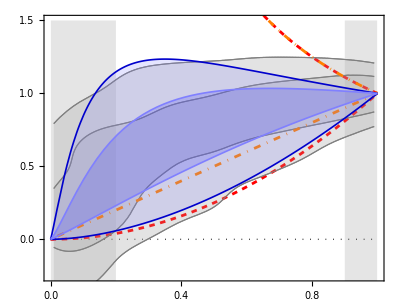

```mathematica
saveThisPlot = False;
plotDC14GlobalBestFit = Show[
  {
    plotBurkertGrayRed /. {Dashed -> Dashing[.01], Black -> Red},
    plotNFWGrayRed /. {Dashed-> DotDashed, Black -> Orange},
    Plot[
      {
        δVDC14[rn, Sequence@@ rsnUpperR @ 2],
        δVDC14[rn, Sequence@@ rsnUpperR @ 1],
        δVDC14[rn, Sequence@@ rsnLowerR @ 2],
        δVDC14[rn, Sequence@@ rsnLowerR @ 1]
      },
      {rn, 0, 1},
      PlotStyle -> {
        {Darker[Blue, 0.2], Thickness @ 0.003},
        {Lighter[Blue, 0.5], Thickness @ 0.003}
      },
      Filling -> {
        1 -> {{3}, Directive[Lighter[Blue, 0.5], Opacity @ 0.2]},
        2 -> {{4}, Directive[Lighter[Blue, 0.2], Opacity @ 0.2]}
      },
      PlotRange -> All
    ]
  }
];

Echo["plotDC14GlobalBestFit:"];
plotDC14GlobalBestFit
savePreviousPlot["plotDC14GlobalBestFit.pdf"];
```

The limiting cases above show the Burkert (red dashed) and NFW (orange dot-dashed) limits.

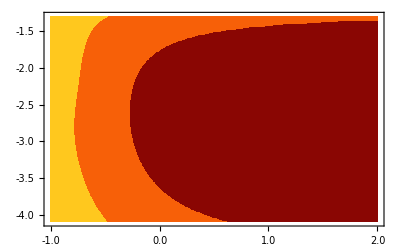

```mathematica
saveThisPlot = False;

min = δVDC14[0.5, 1.91, -1.6];
max = δVDC14[0.5, 0.24, -3.76];

plotRegionDC14low = RegionPlot[
  min > δVDC14[0.5, 10^logrsn, X], {logrsn, -1, 2}, {X, -4.1, -1.3}, 
  PlotPoints-> 100, 
  MaxRecursion->4, 
  Evaluate[generalOptions], 
  BoundaryStyle->None, 
  PlotStyle-> ColorData["SolarColors"][0.05]
];

plotRegionDC14mid = RegionPlot[
  min < δVDC14[0.5, 10^logrsn, X] < max, {logrsn, -1, 2}, {X, -4.1, -1.3}, 
  PlotPoints-> 100, 
  MaxRecursion->4, 
  Evaluate[generalOptions], 
  BoundaryStyle->None, 
  PlotStyle-> ColorData["SolarColors"][0.5]
];

plotRegionDC14high = RegionPlot[
  δVDC14[0.5, 10^logrsn, X] > max, {logrsn, -1, 2}, {X, -4.1, -1.3}, 
  PlotPoints-> 100, 
  MaxRecursion->4, 
  Evaluate[generalOptions], 
  BoundaryStyle->None, 
  PlotStyle-> ColorData["SolarColors"][0.95]
];

Show[plotRegionDC14high, plotRegionDC14mid, plotRegionDC14low, AspectRatio -> 1/GoldenRatio]

savePreviousPlot["plotRegionsDC14.pdf"];
```

### NAV efficiency

```mathematica
efficiencyNAV[δVDC14[#,Sequence@@ rsnLowerR@ 1] &, δVDC14[#, Sequence@@rsnUpperR@ 1] &, 1]
efficiencyNAV[δVDC14[#, Sequence@@rsnLowerR@ 2] &, δVDC14[#, Sequence@@rsnUpperR@ 2] &, 2]
Mean[{%, %%}]
```

{0.775941,0.850244,0.0743022}

{0.824258,0.837723,0.0134646}

{0.8001,0.843983,0.0438834}

## Models CDF analysis

#### CDF comparison using true χ^2 (VChi2)

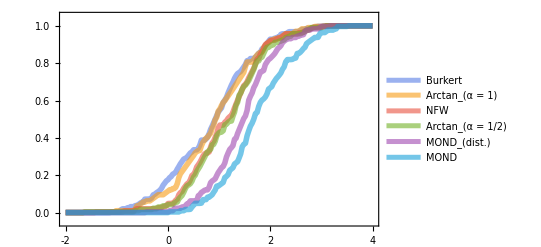

```mathematica
saveThisPlot = False;

SmoothHistogram[{
  Log10@listBurkertVChi2, 
  Log10@listArctanVChi2, 
  Log10@listNFWVChi2, 
  Log10@listArctanHalfVChi2,
  Log10@listMondGDVChi2,
  Log10@listMondVChi2
},
  0.000001, "CDF", 
  PlotRange->{{-2, 4}, {-0.05, 1.05}}, Frame -> True, Axes->False,
  PlotLegends->Placed[{"Burkert", "Arctan_(α = 1)", "NFW", "Arctan_(α = 1/2)", "MOND_(dist.)", "MOND"}, {Left, Center}],   
  PlotStyle-> {{Thickness[0.01], Opacity[0.6]}},
  PlotTheme->{"Scientific", "Frame", "BoldColor"},
  AspectRatio-> 1/GoldenRatio,
  Evaluate[generalOptions]
]

savePreviousPlot["plotCDFcomparison.pdf"];
```

#### CDF comparison for log posterior (effective chi2)

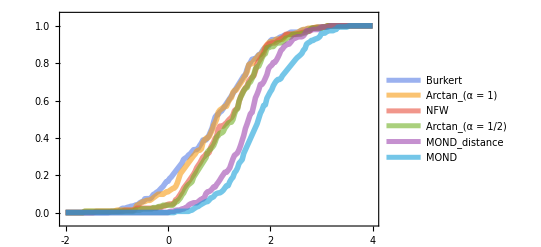

```mathematica
SmoothHistogram[{
  Log10@listBurkertChi2, 
  Log10@listArctanChi2, 
  Log10@listNFWChi2, 
  Log10@listArctanHalfChi2,
  Log10@listMondGDChi2,
  Log10@listMondChi2
},
  0.005, "CDF", 
  PlotRange->{{-2, 4}, {-0.05, 1.05}}, Frame -> True, Axes->False,
  PlotLegends->Placed[{"Burkert", "Arctan_(α = 1)", "NFW", "Arctan_(α = 1/2)", "MOND_distance", "MOND"}, {Left, Center}],   
  PlotStyle-> {{Thickness[0.01], Opacity[0.6]}},
  PlotTheme->{"Scientific", "Frame", "BoldColor"},
  AspectRatio-> 1/GoldenRatio,
  Evaluate[generalOptions]
]
```